```mathematica
(*s=InputString["Enter xml file name","tooth.xml"]//StringReplace[#," "->""]&;*)
xml=Import[NotebookDirectory[]<>"~images\\"<>"vorts1.xml"];
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname,plotpath,imagepath}=xml;
Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]
```

D:\document\work\time-varying-visualization\feature_transfer_function\vortex_naive.tfi
E:\_time_varying_data\vortex_tiff\vorts1.tif
{Feature 1,Feature 2,Feature 3,Feature 4}
top
{D:\document\work\time-varying-visualization\~images\vorts1_saliency_chart.png,D:\document\work\time-varying-visualization\~images\vorts1_visibility_chart.png,D:\document\work\time-varying-visualization\~images\vorts1_visibility_saliency_brightness_chart.png,D:\document\work\time-varying-visualization\~images\vorts1_visibility_saliency_saturation_chart.png,D:\document\work\time-varying-visualization\~images\vorts1_visibility_saliency_weighted_chart.png}
{D:\document\work\time-varying-visualization\~images\vorts1_saliency_chart.txt,D:\document\work\time-varying-visualization\~images\vorts1_visibility_chart.txt,D:\document\work\time-varying-visualization\~images\vorts1_visibility_saliency_brightness_chart.txt,D:\document\work\time-varying-visualization\~images\vorts1_visibility_saliency_saturation_chart.txt,D:\document\work\time-varying-visualization\~images\vorts1_visibility_saliency_weighted_chart.txt}
{D:\document\work\time-varying-visualization\~images\vorts1_visibility_saliency_feature.png,D:\document\work\time-varying-visualization\~images\vorts1_visibility.raw}
D:\document\work\time-varying-visualization\~images\saliency.xml
D:\document\work\time-varying-visualization\~images\vorts1.png
D:\document\work\time-varying-visualization\~images\vorts1.raw
{vorts1}
D:\document\work\time-varying-visualization\~plot\
D:\document\work\time-varying-visualization\~images\

```mathematica
tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;
```

```mathematica
d = Import[volumefile,"Image3D"];
colorized=Image3D[d,ColorFunction->rgbafunction];
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
(*lo=ImageMultiply[lightness,opacity];
co=ImageMultiply[chroma,opacity];*)
(*g1=ImageDifference[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]]
g2=ImageDifference[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]]
g3=ImageDifference[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]];
g4=ImageDifference[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]];*)
{g1,g2}=ParallelMap[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma}];

pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];
chartcolors=rgbcolors[[#]]&/@index;
colorizedfeatures=ImageMultiply[colorized,#]&/@features;
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"."],Show[#,Boxed->False,ViewPoint->viewpoints[face]]]&,colorizedfeatures];

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];
(*Plot[fun[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
(*index0=Flatten@Position[alpha0,_?(#>0&)];*)
```

```mathematica
top:=Module[{list,count,img,list2,list3,d1},(* top *)
list=Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]]
back:=Module[{list,count,img,list2,list3,tmp,d2},(* back *)
list=Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left:=Module[{list,count,img,list2,list3,tmp,d3},(* left *)
list=Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom:=Module[{list,count,img,list2,list3,d4},(* bottom *)
list=Reverse@Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]]
front:=Module[{list,count,img,list2,list3,tmp,d5},(* front *)
list=Reverse@Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right:=Module[{list,count,img,list2,list3,tmp,d6},(* right *)
list=Reverse@Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices=<|"top":>top,"back":>back,"left":>left,"bottom":>bottom,"front":>front,"right":>right|>;
```

```mathematica
top2:=Module[{list,img,list2,list3,df,d1},(* top *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d1=Image3D[list3]
]
back2:=Module[{list,img,list2,list3,tmp,df,d2},(* back *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left2:=Module[{list,img,list2,list3,tmp,df,d3},(* left *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom2:=Module[{list,img,list2,list3,df,d4},(* bottom *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d4=Image3D[Reverse[list3]]]
front2:=Module[{list,img,list2,list3,tmp,df,d5},(* front *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right2:=Module[{list,img,list2,list3,tmp,df,d6},(* right *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices2=<|"top":>top2,"back":>back2,"left":>left2,"bottom":>bottom2,"front":>front2,"right":>right2|>;
```

```mathematica
Clear[f];
Clear[data];
vis=Block[{f=fun,data=d},renderslices2[face]];
```

{0.900583,0.0833394,0.0160776}

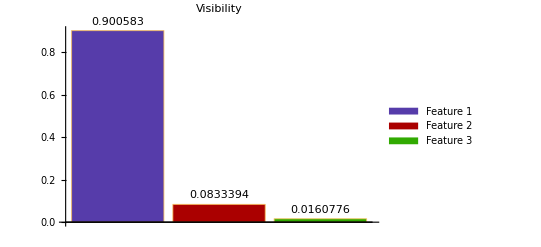

{0.428693,0.091112,0.0628314}

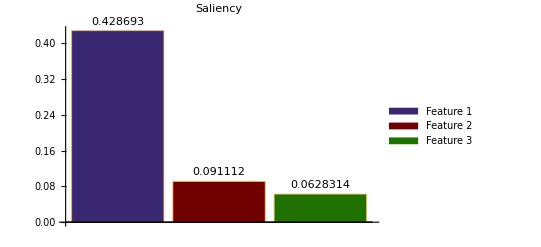

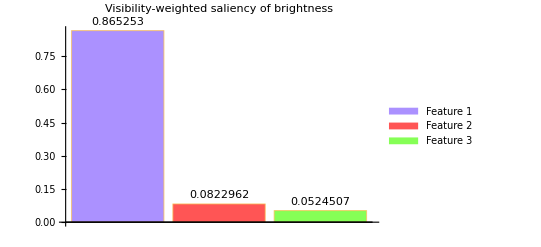

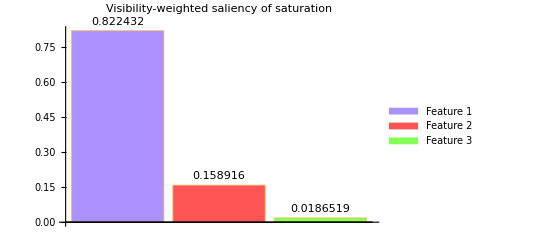

{0.843843,0.120606,0.0355513}

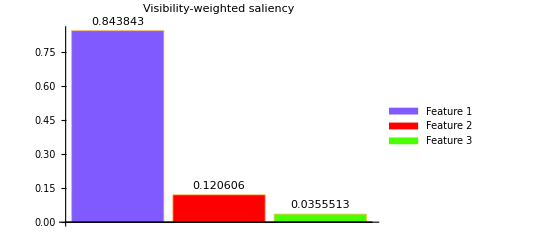

```mathematica
visibility=ParallelTable[ImageMeasurements[ImageMultiply[vis,features[[i]]],"TotalIntensity"]/ImageMeasurements[vis,"TotalIntensity"],{i,Length[features]}]
chart1=BarChart[visibility,PlotLabel->"Visibility",ChartLegends->legends,ChartStyle->Darker@chartcolors,ChartLabels->Placed[ToString/@visibility,Above]]
dog=g1;
saliency=ParallelTable[ImageMeasurements[ImageMultiply[dog,features[[i]]],"TotalIntensity"]/ImageMeasurements[dog,"TotalIntensity"],{i,Length[features]}]
chart0=BarChart[saliency,PlotLabel->"Saliency",ChartLegends->legends,ChartStyle->Darker@Darker@chartcolors,ChartLabels->Placed[ToString/@saliency,Above]]
viss=ImageMultiply[g1,vis];(* weighted by lightness DoG (difference of Gaussians) *)
(*vs=Table[ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,features}];*)
total=ImageMeasurements[viss,"TotalIntensity"];
vs=ParallelTable[If[total≠0,ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/total,0],{i,features}];
chart2=BarChart[vs,PlotLabel->"Visibility-weighted saliency of brightness",ChartLegends->legends,ChartStyle->Lighter@chartcolors,ChartLabels->Placed[ToString/@vs,Above]]
viss2=ImageMultiply[g2,vis];(* weighted by chroma DoG *)
(*vs2=Table[ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,features}];*)
total2=ImageMeasurements[viss2,"TotalIntensity"];
vs2=ParallelTable[If[total2≠0,ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/total2,0],{i,features}];
chart2b=BarChart[vs2,PlotLabel->"Visibility-weighted saliency of saturation",ChartLegends->legends,ChartStyle->Lighter@chartcolors,ChartLabels->Placed[ToString/@vs2,Above]]
mean=Mean[{vs,vs2}]
weighted=BarChart[mean,PlotLabel->"Visibility-weighted saliency",ChartLegends->legends,ChartStyle->chartcolors,ChartLabels->Placed[ToString/@mean,Above]]
charts={chart0,chart1,chart2,chart2b,weighted};
scores={saliency,visibility,vs,vs2,mean};
Table[Export[imagefilenames[[i]],charts[[i]]],{i,Length[charts]}];
(*Table[Export[txtfilenames[[i]],scores[[i]]],{i,Length[scores]}];*)
scoremap=If[FileExistsQ[resultxml],Association@Import[resultxml],<||>];
AssociateTo[scoremap,dataname->scores];
Export[resultxml,Normal[scoremap]];
w=ImageAdd[viss,viss2]//ImageAdjust;
results=ImageMultiply[w,#]&/@features;
MapIndexed[Export[StringReplace[featurefilename,"."->ToString[First[#2]]<>"."],#]&,results];
```

```mathematica
(*Export[path<>"Tooth_RGBA.raw",Flatten@ImageData[r,"Byte"],{"Binary","Byte"}];
Export[path<>"Tooth_"<>StringTake["RGBA",{#}]<>".raw",Flatten@ImageData[ColorSeparate[r,"RGBA"][[#]],"Byte"],{"Binary","Byte"}]&/@Range[4];
s="NDims = 3
DimSize = 140 120 161
ElementType = MET_UCHAR
ElementSpacing = 1.0 1.0 1.0
ElementByteOrderMSB = False
ElementDataFile = Tooth_.raw\n";
Export[path<>"Tooth_"<>StringTake["RGBA",{#}]<>".mhd",StringReplace[s,"Tooth_"->"Tooth_"<>StringTake["RGBA",{#}]],"Text"]&/@Range[4];*)
(*Export[visibilityfilename,Flatten@ImageData[vis,"Byte"],{"Binary","Byte"}];*)
Image3D[d,ColorFunction->rgbafunction,ViewPoint->viewpoints[face]]
```